```mathematica
expectedSpeedup[n_]:= 1/(0.01+0.99/n)
```

```mathematica
expectedSpeedup[2]
```

1.9802

```mathematica
data = {{1, 1.78504},{2,0.9445},{4,},{8,},{16,}}
```

```mathematica
PlotRange[]
```

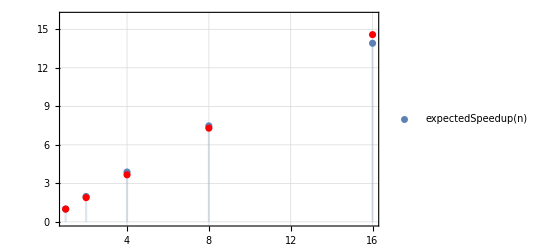

```mathematica
Show[
DiscretePlot[expectedSpeedup[n],{n,{1,2,4,8,16}},  PlotTheme->"Detailed"],
ListPlot[{{1, 1},{2,1.78504/0.9445},{4,1.78504/0.4865},{8,1.78504/0.2445},{16,1.78504/0.1224}}, PlotStyle->Red],
PlotRange-> {0,16}
]
```